```mathematica
littlewood[n_Integer,x_:x]:=1+Tuples[{1,-1},n]. x^Range[n]
```

```mathematica
littlewood[3]//Column//TraditionalForm
```

x^3+x^2+x+1
-x^3+x^2+x+1
x^3-x^2+x+1
-x^3-x^2+x+1
x^3+x^2-x+1
-x^3+x^2-x+1
x^3-x^2-x+1
-x^3-x^2-x+1

```mathematica
littlewoodRoots[n_]:= ComplexListPlot[x/. Solve[Times @@ littlewood[n]==0, x]]
```

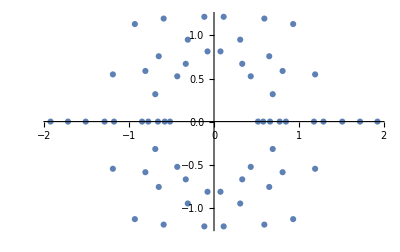

```mathematica
littlewoodRoots[4]
```

#### A fancier function with a slight increase in speed:

```mathematica
fastRootCalculate[n_Integer,x_:Unique[]]:=With[{
poly=1+Map[{1}~Join~#&,Tuples[{1,-1},n-1]]. #^Range[n]&,
solve=If[$VersionNumber<12.3,x/.NSolve@##&,NSolveValues],
mirror=If[n>3,Thread,Identity]@Join[#,-#]&,
map=If[n>5,ParallelMap,Map],
k=Floor[n/4]-$KernelCount},
If[k>0,LaunchKernels@k];
map[solve[#==0,x]&,poly@x]//mirror]
```

```mathematica
Block[{r,k=4-$KernelCount},If[k>0,LaunchKernels@k];
AbsoluteTiming[r=fastRootCalculate[10];]]
```

{0.428502,Null}

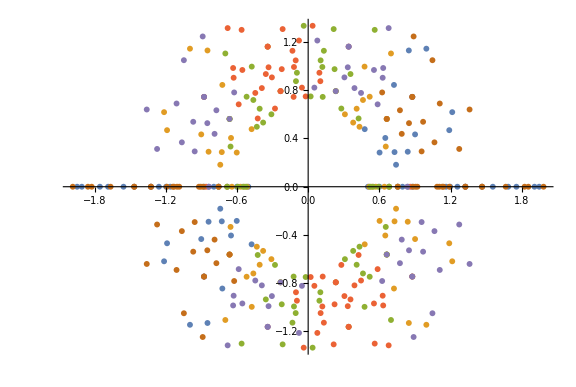

```mathematica
ComplexListPlot[fastRootCalculate[6],ImageSize->Large]
```

```mathematica
displayRoots[n_]:=With[{
p=fastRootCalculate[n],
c=Hue[#/n,1,1,If[n>12&&n<15,.3n-3.4,1]]&~Array~n,
s=AbsolutePointSize@If[n>15,1/(n-14),16-n],
r=PlotRange->4.1{#,#}2^-{1,3/2}&[{-1,1}],
l=PlotLabel->Style[Row@{"n = ",n},FontSize->(n+7)3],
w=ImageSize->(n+7)125},
With[{a=If[n>5,MapThread[{#1,Point@ReIm[#2]}&,{c,p}],
AspectRatio->Tr@Ratios[Differences/@Last@r]]},
If[n>5,Graphics[Flatten@{s,a},w,r,l],
ComplexListPlot@@{p,PlotStyle->s,w,r,a,l}]]
]
```

```mathematica
Block[{r},AbsoluteTiming[r=fastRootCalculate@18;]]
```

{139.917,Null}

```mathematica
Block[{g=Table[Graphics[],19],a=AbsoluteTiming,t},
With[{k=Floor[Length@g/4]-$KernelCount},If[k>0,LaunchKernels@k]];
t=Table[{0,0},Length@g+1];
Do[t[[i]]=First/@{
a[g[[i]]=displayRoots[i];],
a[Export[ToString@i<>".png",g[[i]]];]},{i,Length@g}];
CloseKernels[];
t[[-1]]=First/@{
a[g=With[{l=7+Length@g},Magnify~MapThread~{g,l/Range[8,l]}];],
a[Export["root.gif",g,"DisplayDurations"->3/2];]};
With[{h= {n,"Calculations","Graphics"}},Column@{"",
Style["Timing Values (sec):",FontSize->14,FontWeight->Bold],"",
TableForm[MapIndexed[#2~Join~#1&,t],TableHeadings->{None,h}]}]
]
```

Timing Values (sec):

n | Calculations | Graphics
1 | 0.397289 | 0.752304
2 | 0.0365289 | 0.257025
3 | 0.0450592 | 0.287978
4 | 0.0632728 | 0.339383
5 | 0.0693781 | 0.37985
6 | 0.046266 | 0.437164
7 | 0.0634543 | 0.50326
8 | 0.10779 | 0.577492
9 | 0.222004 | 0.711352
10 | 0.434687 | 0.933041
11 | 0.843347 | 1.2992
12 | 1.73426 | 2.16915
13 | 3.43867 | 3.27961
14 | 7.12681 | 5.53685
15 | 14.7044 | 10.6169
16 | 31.5234 | 21.9042
17 | 66.9807 | 51.8926
18 | 139.379 | 99.4805
19 | 297.642 | 220.629
20 | 0.0023634 | 399.483